# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-4,30-4}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

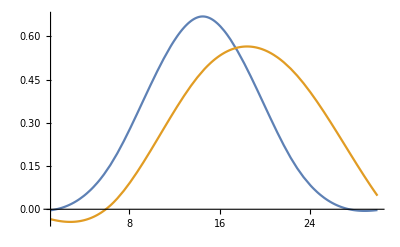

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Block[{n,fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

n=0;

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=1*dfline1'[p1];
fric2=1*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<n,Return[{v1,v2,"sign",e+1}],Return[{0.,0.,"sign",e}]]];

(* magnitud *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<n,Return[{v1,v2,"mag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

If[e<=n,{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.01,"converged","ok"],e},Return[{0.,0.,status,e}]]

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.5,3,"ok",0.};
i=0;
p=11;
```

```mathematica
n=3;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,noteBookMode]
```

{1.49568,2.50444,converged,0.}

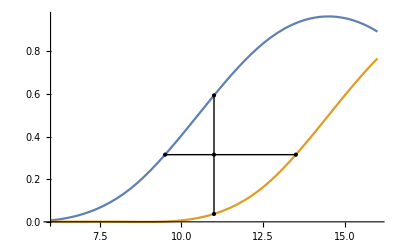

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)

newValues[i_,{v1_,v2_,status_,e_},newv0_,"ConstrainedNewMethod"]:=Block[{n,v,r,rs},(
v=v1+v2;
n=0;

If[e>n,
Return[{{0.,0.}}];
];

If[v≠0. && status=="ok",
Table[
r=RandomReal[];
{r,1-r}*v
,{j,i}]
,
newv0
]

)]
```

```mathematica
(* We create the list of values in case v=0 *)
r=RandomReal[];
rangev0=Range[0,5,0.2];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];
```

```mathematica
nV=newValues[10,{1.,1.,"sign",1.},newv0,"ConstrainedNewMethod"]
Total/@nV
```

{{0.,0.}}

{0.}

```mathematica
(* This will give back a value that converged or is on "ok" status. If not, error is returned and {v1,v2} goes back to 0. *)

pickNewValue[tableNewVals_,"ConstrainedNewMethod"]:=Block[{newValCon,newValAny},(

newValCon=Select[tableNewVals,(#[[3]]==("converged")&& #[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];
newValAny=Select[tableNewVals,(#[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];

If[newValCon=={}&&newValAny=={},
tableNewVals[[1]]
,

If[newValCon=={},

If[newValAny[[1,3]]!="converged",
newValAny[[1]],
Flatten[{0.,0.,"fakeconverged",newValAny[[1,4]]+1}]
],

newValCon[[1]]
]

]
)]
```

```mathematica
threshold=0.001;
n=1;
p0=23;
i=10;

updateValues={0.,0.,"ok",0.};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)

nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNV=Table[
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),noteBookMode]

,{j,1,i}];

tValues
,{v,nV}];

sol=pickNewValue[tableNV,"ConstrainedNewMethod"]
```

{3.87506,0.0965616,converged,0.}

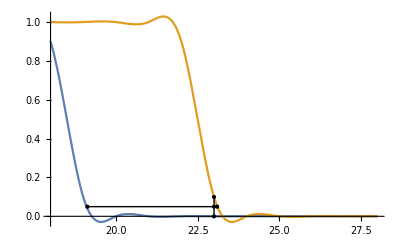

```mathematica
(* see *)
seePlot[p0,5,sol[[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_,listv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{n,c, updateValues,nV,tableNewValues,tValues},(

n=0;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Do[


(* Flag to stop when e≥n *)
If[updateValues[[4]]<=n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;4]],listv0,"ConstrainedNewMethod"];
(* compute at this scale, using current motion estimate *)

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[
tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"];
If[tValues[[3]]!="ok",Break[]];

,{j,1,i}];

tValues
,{v,nV}];

(* We only update updateValues with the tValue that converged *)
updateValues=pickNewValue[tableNewValues,"ConstrainedNewMethod"];


c=c-1;
,{f,1,Length[pyrfunctions]}];

updateValues[[1;;3]]
)];
```

#### Test

```mathematica
p=14;
```

{{0.,0.,mag,1},{0.,0.,sign,2},{0.,0.,mag,3},{0.,0.,mag,4},{0.,0.,sign,5},{0.,0.,mag,6},{0.020001,3.98007,converged,7},{0.,0.,sign,8},{0.981569,3.01957,converged,9},{0.0867928,3.91547,converged,10},{0.554935,3.44508,converged,11},{1.49997,2.50003,converged,12},{2.50009,1.49991,converged,13},{3.44638,0.553619,converged,14},{3.87734,0.121697,converged,15},{2.00777,1.99038,converged,16},{1.9899,2.01056,converged,17},{0.10804,3.86788,converged,18},{0.554656,3.44534,converged,19},{1.50001,2.49999,converged,20},{2.50003,1.49997,converged,21},{3.44635,0.55363,converged,22},{3.87937,0.121446,converged,23},{2.01881,1.98438,converged,24},{2.,4.61312×10^-18,converged,25},{3.0198,0.985461,converged,26},{3.97749,0.0250928,converged,27},{0.,0.,sign,28},{0.,0.,mag,29},{0.,0.,sign,30}}

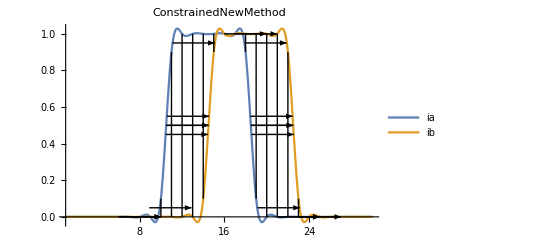

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[newv0,Range[1,30],pyrf12[[1;;2]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[newv0,Range[1,30],pyrf12[[1;;2]],0.001,noteBookMode]
```

#### Test

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[newv0,Range[p-5,p+5],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[newv0,Range[p-5,p+5],pyrf12[[1;;4]],0.001,noteBookMode]
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
{v1, v2,status,e}={0.5,3,"ok",0.};
i=40;
p=15;

(* m-> max lvl, n-> min lvl *)
m=2;
n=2;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,{{0.5,3}},pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[newv0,Range[1,Length[line1]],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

## Graphics for One pixel

```mathematica
pickNewValueIter[tableIterNewVals_,"ConstrainedNewMethod"]:=Block[{newIterValCon,newIterValAny},(
newIterValCon=Select[tableIterNewVals,(Last[#][[3]]==("converged")&&Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];
newIterValAny=Select[tableIterNewVals,(Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];

If[newIterValCon=={}&&newIterValAny=={},
tableIterNewVals[[1]]
,

If[newIterValCon=={},

If[Last[newIterValAny[[1]]][[3]]≠"converged",
newIterValAny[[1]],
Join[newIterValAny[[1]],{Flatten[{0.,0.,"fakeconverged",Last[newIterValAny[[1]]][[4]]+1}]}]
]
,
newIterValCon[[1]]
]

]

)]
```

```mathematica
i=10;
p0=10;
threshold=0.001;
n=3;
updateValues={0.,0.,"ok",0.};
```

```mathematica
(* Flag to stop when e≥2 *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 5 and -5 *)
nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"][[All,1;;3]]

Last[goodValIter]
```

```mathematica
(* see *)
seePlot[p0,5,Last[goodValIter][[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,newv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,tValues,iterTable,goodValIter,nV},(

n=1;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Table[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"];
updateValues=Last[goodValIter];

goodValIter[[All,1;;3]]
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]
,{p,1,30}]
```

```mathematica
Table[
PyrFlow1DIter[10,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]==PyrFlow1DIter[10,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

#### Test

```mathematica
(* List of initial values we are going to try *)
ListPlot[newv0]
```

```mathematica
seeAllLine[newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[0,5,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

```mathematica
lvlmin=1;
lvlmax=3;
p=15;
dis=4;

mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,p,listv0,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";

(*pixelInitialValueGraphics[10,1000,p,{-10,10},dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]*)
```